# MATH299M/CMSC389W - Visualization through Mathematica Week 2: Basics II: Defining Functions, Implicit Functions, Table, Map

Lists, Tuples, and Sets

The primary data structure for storing linear data in Mathematica is the list. Lists in Mathematica can contain any number of items.

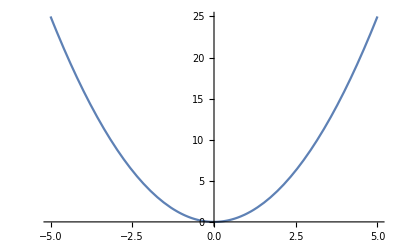
{1,Apple,-Graphics-}

```mathematica
{1,"Apple",Plot[x^2,{x,-5,5}]}
```

```mathematica
{1,2,3}; (* Lists are denoted with curly brackets *)
{}; (* Empty list *)
{1} (* Singleton list *)
{{},{1},{2},{1,2}};(* list of lists *)
{{{{5}}}}; (* List of lists of lists of lists of a number *)
```

{1}

The middle line doesn’t have a semicolon to show you that you can do that, and to show what lists look like in output.

```mathematica
"Ajeet"=="Ajeet"
```

True

```mathematica
{1,1,2,3}=={1,2,3}
```

False

Lists are indexed using double square brackets. Lists are 1-index and also support range and negative indexing.

```mathematica
lst={{"Apple","Orange","Dragon Fruit","Mango"},{"Rock","Paper","Scissors"}}
```

{{Apple,Orange,Dragon Fruit,Mango},{Rock,Paper,Scissors}}

```mathematica
lst[[1]]
lst[[-1]]
lst[[1,1;;3]]
```

{Apple,Orange,Dragon Fruit,Mango}

{Rock,Paper,Scissors}

Message::name: Message name MessageName[1,3] is not of the form symbol::name or symbol::name::language.

Part::pkspec1: The expression MessageName[1,3] cannot be used as a part specification.

{{Apple,Orange,Dragon Fruit,Mango},{Rock,Paper,Scissors}}⟦1,MessageName[1,3]⟧

```mathematica
{{"Apple","Orange","Dragon Fruit","Mango"},{"Rock","Paper","Scissors"}}[[1,3]]
```

Dragon Fruit

List operations (and an aside on types, or lack thereof)

First off take note that a list can contain a mixture of types of objects, Mathematica in general doesn’t really care about types. You can use types in a certain context, but they’re not really relevant, in Mathematica you shouldn’t worry about types and instead just write your code with explicit documentation so that the user knows what is supposed to come in an and out of those functions. For any function you can theoretically put anything in the Mathematica language in there - for example, later we’ll use Plots which are graphs, Mathematica would have no problem with you making a list of Plots.

```mathematica
Length[{"Apple",5,"α",True,"Kiwi"}]
```

5

```mathematica
Length[{}]
```

0

```mathematica
Length[{{1,2},{3,4,5}}] (* The length of a list of lists is, of course, the number of inner lists *)
```

2

We can grab an element from a list by index by putting the index in double brackets after the set. Mathematica list indexing starts at 1.

```mathematica
FruitList={"Apple","Mango","Kiwi","Passion Fruit","Durian"};
FruitList[[3]]
```

Kiwi

Or by specifying a list we can grab multiple objects, repeats are okay because they’re lists:

```mathematica
FruitList[[{2,4,5}]]
```

{Mango,Passion Fruit,Durian}

```mathematica
FruitList[[{1,1,3,1,5}]]
```

{Apple,Apple,Kiwi,Apple,Durian}

And multiple arguments in the double brackets we can specify objects from levels of lists, you can think of this as grabbing elements from an array. Here’s an example of grabbing elements from a 2D array:

```mathematica
VeggieList={"Carrot","Onion","Pepper","Cucumber","Broccoli","Radish"};
Legumes={"Soybean","Lentil","Edamame","Chickpea"};
FruitsAndVeggies={FruitList,VeggieList,Legumes}
```

{{Apple,Mango,Kiwi,Passion Fruit,Durian},{Carrot,Onion,Pepper,Cucumber,Broccoli,Radish},{Soybean,Lentil,Edamame,Chickpea}}

```mathematica
FruitsAndVeggies[[2,1]]
```

Carrot

```mathematica
FruitsAndVeggies[[3,3]]
```

Edamame

As before, you can use sets to grab multiple elements. If you, for example, specify 2 elements in the first argument and 3 in the second, you’ll get the elements from those three indices of both lists you specified with the first argument, for a result of a nested list with 3 pairs of elements.

```mathematica
FruitsAndVeggies[[{1,3},1]]
```

{Apple,Soybean}

```mathematica
FruitsAndVeggies[[{1,2,3},{3,4}]]
```

{{Kiwi,Passion Fruit},{Pepper,Cucumber},{Edamame,Chickpea}}

```mathematica
FruitsAndVeggies[[{1,3},{1}]]
```

{{Apple},{Soybean}}

We can also count the number of a certain element in a list, remove certain elements, and remove all duplicates.

```mathematica
PiList={3,1,4,1,5,9,2,6,5,3,5,8,9,7,9,3,2,3,8,4,6,2,6,4};
Count[PiList,3]
```

4

```mathematica
DeleteCases[PiList,4]
```

{3,1,1,5,9,2,6,5,3,5,8,9,7,9,3,2,3,8,6,2,6}

```mathematica
DeleteDuplicates[PiList]
```

{3,1,4,5,9,2,6,8,7}

Here are a bunch more useful functions whose names are pretty self explanatory. Notice that the output of these functions doesn’t change the actual list fed as an argument, it spits out a new object. If you want to change the value of a list you need to reassign the output of the function to the variable.

```mathematica
Maths={"Algebra","Analysis","Geometry","Toplogy","Combinatorics"};
Prepend[Maths,"Stats"] (* The thing to prepend is the second argument *)
```

{Stats,Algebra,Analysis,Geometry,Toplogy,Combinatorics}

```mathematica
Append[Maths,"Stats"]
```

{Algebra,Analysis,Geometry,Toplogy,Combinatorics,Stats}

```mathematica
Insert[Maths,"Stats",2]
```

{Algebra,Stats,Analysis,Geometry,Toplogy,Combinatorics}

```mathematica
Insert[Maths,"Stats",-2] (* Using a negative integer for the third argument will insert in that position from the right *)
```

{Algebra,Analysis,Geometry,Toplogy,Stats,Combinatorics}

```mathematica
Delete[Maths,2] (* Delete element at a certain index *)
```

{Algebra,Geometry,Toplogy,Combinatorics}

```mathematica
ReplacePart[Maths,1->"Abstract Algebra"] (* Use an arrow to indicate which index is being changed to whatever's on the RHS of the arrow *)
```

{Abstract Algebra,Analysis,Geometry,Toplogy,Combinatorics}

Some other strangely useful functions are Flatten, Riffle, Partition. Flatten is of extreme importance, you’ll end up using it very frequently.

```mathematica
FruitsAndVeggies
```

{{Apple,Mango,Kiwi,Passion Fruit,Durian},{Carrot,Onion,Pepper,Cucumber,Broccoli,Radish},{Soybean,Lentil,Edamame,Chickpea}}

The Join function is extremely important, it’s the best way to concatenate lists together.

```mathematica
Join[{1,2,3},{4,5,6}]
```

{1,2,3,4,5,6}

```mathematica
Join[{1,1,1,2},{5,6,7},{1,1,2,1}]
```

{1,1,1,2,5,6,7,1,1,2,1}

```mathematica
Flatten[FruitsAndVeggies] (* Flatten collapses down all levels of brackets, for a 2D array that means just unioning the rows of the array *)
```

{Apple,Mango,Kiwi,Passion Fruit,Durian,Carrot,Onion,Pepper,Cucumber,Broccoli,Radish,Soybean,Lentil,Edamame,Chickpea}

```mathematica
Flatten[{{{1},{2,3}},{4,5,6},{{{{{7}}}}}}]
```

{1,2,3,4,5,6,7}

```mathematica
Flatten[{{{{1},{2}},{{3},{4}}},{{{5},{6}},{{7},{8}}}},1] (* The second argument can be used to specify how many levels you want to break down. *)
```

{{{1},{2}},{{3},{4}},{{5},{6}},{{7},{8}}}

```mathematica
Flatten[{{{{1},{2}},{{3},{4}}},{{{5},{6}},{{7},{8}}}},2]
```

{{1},{2},{3},{4},{5},{6},{7},{8}}

```mathematica
Flatten[{{{{1},{2}},{{3},{4}}},{{{5},{6}},{{7},{8}}}},3]
```

{1,2,3,4,5,6,7,8}

```mathematica
Riffle[{1,2,3},{"a","b","c"}] (* Interleaves the elements of two lists *)
```

{1,a,2,b,3,c}

```mathematica
Riffle[{1,2,3,4,5,6,7,8},{True,False}] (* Cycles through second list if it's smaller than the first *)
```

{1,True,2,False,3,True,4,False,5,True,6,False,7,True,8}

```mathematica
Partition[{1,2,3,4,5,6,7,8,9,10},2] (* Breaks up list into sets of the size specified in the second argument *)
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

```mathematica
Partition[{1,2,3,4,5,6,7,8,9,10},3] (* Leftovers are discarded *)
```

{{1,2,3},{4,5,6},{7,8,9}}

Here we have set operations that treat the lists like sets in the sense that duplicates are removed. However for all of these algorithms order is preserved.

```mathematica
Set1={1,2,3,4,5,6};
Set2={5,6,7,8,9,10};
Union[Set1,Set2] (* Notice that there aren't two copies of 5 and 6 in the result *)
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Intersection[Set1,Set2]
```

{5,6}

And here’s some subset stuff. Notice that I say “set” in the comments - I mean this! Take a look, there aren’t any tuples in the output that contain the exact same values in a different order.

```mathematica
Subsets[{1,2,3,4}] (* Returns the power set of the argument *)
```

{{},{1},{2},{3},{4},{1,2},{1,3},{1,4},{2,3},{2,4},{3,4},{1,2,3},{1,2,4},{1,3,4},{2,3,4},{1,2,3,4}}

```mathematica
Subsets[{1,2,3,4},2](* Returns all susbets of up to a certain size *)
```

{{},{1},{2},{3},{4},{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}}

```mathematica
Subsets[{1,2,3,4},{2}](* Returns all subsets of exactly a certain size *)
```

{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}}

Range generates a list of numbers for you

```mathematica
Range[5] (* Generates integers from 1 to the argument *)
Range[2,7] (* Generate integers between arguments *)
Range[-1,2,.5] (* Generates numbers between first two arguments at step size of third argument *)
```

{1,2,3,4,5}

{2,3,4,5,6,7}

{-1.,-0.5,0.,0.5,1.,1.5,2.}

Map

Map is your best friend! Besides Table, Table and Map are your best friends. Really they do the exact same thing, so you can choose which one you want to be best friends with, but keep the other one close. Anyway, Map takes in two arguments, a function and a list, and then it returns the function applied to every element of that list, very useful for doing a lot of computations quickly. After being exposed to this tool it’s going to feel barbaric to do a lot of things by hand anymore.

```mathematica
Square[x_]:=x^2;
Map[Square,{1,2,3,4,5}]
```

{1,4,9,16,25}

```mathematica
Map[Sin,π/4*Range[0,16]] (*Range is inclusive on both 0 and 16 [0, 16]*)
```

{0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0,1/(√2),1,1/(√2),0,-1/(√2),-1,-1/(√2),0}

Map has an alternate notation using /@, which I don’t prefer, but it exists:

```mathematica
Square/@{1,2,3,4}
```

{1,4,9,16}

Table

Table is given an argument that is a statement with a variable and then an argument that is a tuple containing a variable of iteration, a start, an end, and then an optional element that is the step size, defaulted to 1, and then outputs a list of the statement evaluated for each term of the variable iterated through, so a For loop:

```mathematica
Table[n,{n,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Table[n^2,{n,1,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[n^2,{n,1,10,2}]
```

{1,9,25,49,81}

```mathematica
Table[n^2+n,{n,1,10,1}](* It's my personal style to put the redundant 1 for the step size in the iterator tuple for table, but you by no means need to do this *)
```

{2,6,12,20,30,42,56,72,90,110}

You can give it a second (or third, etc.) iterator tuple to iterate through another variable once it’s completed the first, so like nested For loops:

```mathematica
Table[x*y,{x,1,4},{y,1,4}]
```

{{1,2,3,4},{2,4,6,8},{3,6,9,12},{4,8,12,16}}

```mathematica
Table[Table[x*y,{x,1,4}],{y,1,4}] (* This is equivalent to the form above *)
```

{{1,2,3,4},{2,4,6,8},{3,6,9,12},{4,8,12,16}}

You can also use Table to iterate a variable over a specific set through a slight change in notation where in the iterator tuple the second element is the list to iterate over:

```mathematica
Table[n^2,{n,{1,1,2,3,5,8}}]
```

{1,1,4,9,25,64}

Even if it doesn’t seem like it right now, these functions are going to prove EXTREMELY useful to you - or maybe not, I know that my style of coding relies on them heavily, maybe yours won’t! I’m interested to see. Anyway, to drive the point home of how these are the same thing, I’ll write them in each other; part of MyTable you won’t understand until the next section on implicit functions, but that’s okay, you can come back to it:

```mathematica
MyMap[foo_,lst_]:=Table[foo[var],{var,lst}];
MyMap[Square,{1,2,3}]
```

{1,4,9}

```mathematica
MyTable[body_,{var_,lst_}]:=Map[(body/.{var->#})&,lst]; 
MyTable[Square[n],{n,{1,2,3}}]
```

{1,4,9}

Implicit (Pure) Functions

Implicit functions and Apply are great to know - it makes it so whatever you need to happen you can do. Sometimes doing things the right way is a headache but it’s important to know what you can do.

Functions are objects that are basically rules that take in input and produce a corresponding output. In Mathematica we can construct these function objects without giving them names for cases where we only need to use the function once, it often makes for more elegant and concise code than introducing helper functions. An implicit function is always terminated with a &, and before that any instance where the input to the function is to go is denoted by a #. Mathematica calls them “pure functions” in the documentation, “implicit functions” is just what I like to call them. Here’s an example of a function being called in Table and it’s implicit version:
The biggest benefit is you do not have to define a name for your function, you just declare it and use it.

```mathematica
Cube[x_]:=x^3;
Map[Cube,{1,2,3,5,8,13}]
```

{1,8,27,125,512,2197}

```mathematica
Map[(#^3)&,{1,2,3,5,8,13}]
```

{1,8,27,125,512,2197}

```mathematica
Foo[x_]:=x^2+x;
Map[Foo,{1,2,3,5,8,13}]
```

{2,6,12,30,72,182}

```mathematica
Map[(#^2+#)&,{1,2,3,5,8,13}]
```

{2,6,12,30,72,182}

Here we use a new function called Apply, which takes in a function and a tuple and then applies the elements of that tuple as the arguments of the function.

```mathematica
Pow[x_,y_]:=x^y;
Apply[Pow,{2,3}]
```

8

```mathematica
Map[Apply[Pow,#]&,{{1,1},{2,3},{3,5}}]
```

{1,8,243}

We can also implicitly define functions of multiple variables by using numbers after the hashes to indicate which argument we’re referring to, #1,#2, etc. The only time I’ve personally ever used this is with the Fold function though, see below.

Fold

Fold is a very useful function that pairs nicely with map and is among the basic tools coders know how to use in (basically) any language they learn. It takes three arguments, a function, a starting variable, and a list. The function takes in two values, the first is always an accumulator, something that changes step to step, and the second argument iterates through the list; the function returns the new value of the accumulator, and the starting variable is what the accumulator starts at.

```mathematica
Add[total_,addend_]:=total+addend;
Fold[Add,0,{1,2,3,4,5,6,7,8,9,10}]
```

55

<> Is the concatenation operation for Mathematica String

```mathematica
Sentence[sent_,word_]:=sent<>" "<>word;
Fold[Sentence,"",{"Mathematica","is","awesome!"}]
```

Mathematica is awesome!

Here are implicit versions of these applications of fold, that is, without explicitly defining the helper function:

```mathematica
Fold[(#1+#2)&,0,{1,2,3,4,5,6,7,8,9,10}]
```

55

```mathematica
Fold[(#1<>" "<>#2)&,"",{"Mathematica","is","awesome!"}]
```

Mathematica is awesome!

Fold is a recursive function, writing it may be illuminating as to exactly how it works:

```mathematica
MyFold[f_,acc_,{}]:=acc;
MyFold[f_,acc_,lst_]:=MyFold[f,f[acc,lst[[1]]],Delete[lst,1]];

MyFold[(#1+#2)&,0,{1,2,3,4,5,6,7,8,9,10}]
MyFold[(#1<>" "<>#2)&,"",{"Mathematica","is","awesome!"}]
```

55

Mathematica is awesome!

## Ajeet Gary - University of Maryland Experimental Geometry Lab MATH299M/CMSC389W Fall 2018 September 1st, 2018

## Vlad Dobrin - University of Maryland Computer Science MATH299M/CMSC389W Spring 2020 January 2nd, 2020